# The Student’s Introduction to Mathematica

## A Handbook for Precalculus, Calculus, and Linear Algebra

## Chapter 1: Getting Started

## 1.4 Commands for Basic Arithmetic

```mathematica
2+2
```

4

```mathematica
17+1
```

18

```mathematica
17-1
```

16

```mathematica
123456789*123456789
```

15241578750190521

```mathematica
123456789 123456789
```

15241578750190521

```mathematica
123456789^2
```

15241578750190521

```mathematica
9.1/256.127
```

0.0355292

```mathematica
34/4
```

17/2

```mathematica
(1/2)^6
```

1/64

## 1.6 The Basic Math Assistant Palette

```mathematica
17^19
```

239072435685151324847153

```mathematica
17^19
```

239072435685151324847153

```mathematica
(1+x)^8
```

(1+x)^8

```mathematica
(1+x)^8
```

(1+x)^8

```mathematica
50653^(1/3)
```

37

```mathematica
50653^(1/3)
```

37

```mathematica
37^3
```

50653

```mathematica
√50653≤225
```

False

```mathematica
√50653≤226
```

True

```mathematica
√50653==50653^(1/2)
```

True

## 1.7 Decimal In, Decimal Out

```mathematica
17^19/19^17
```

239072435685151324847153/5480386857784802185939

```mathematica
59875^(1/3)
```

5 479^(1/3)

```mathematica
17.0^19/19^17
```

43.6233

```mathematica
59875.0^(1/3)
```

39.1215

```mathematica
17.^19/19^17
```

43.6233

```mathematica
59875.^(1/3)
```

39.1215

```mathematica
30/2
```

15

## 1.8 Use Parentheses to Group Terms

```mathematica
3*(4+1)
```

15

```mathematica
3*4+1
```

13

```mathematica
(-3)^2
```

9

```mathematica
-3^2
```

-9

```mathematica
(3+1)/2
```

2

```mathematica
3+1/2
```

7/2

```mathematica
(3+1)/2
```

2

```mathematica
3+1/2
```

7/2

```mathematica
25(2+2)
```

100

## 1.9 Three Well-Known Constants

```mathematica
π
```

π

```mathematica
π+0.
```

3.14159

ESC+p+ESC for π, ESC+ee+ESC for ⅇ, ESC+ii+ESC for ⅈ
Also, type Pi for π, E for ⅇ, and I for ⅈ

```mathematica
I^2
```

-1

```mathematica
Log[E]
```

1

```mathematica
Cos[Pi]
```

-1

```mathematica
π^(1/3)
```

π^(1/3)

```mathematica
π^(1/3)
```

π^(1/3)

```mathematica
Pi==π
```

True

## 1.10 Typing Commands in Mathematica

### Numerical approximation

```mathematica
N[π]
```

3.14159

```mathematica
17^30
```

8193465725814765556554001028792218849

```mathematica
N[17^30]
```

8.19347×10^36

```mathematica
N[1/2^50]
```

8.88178×10^-16

```mathematica
N[17^30,20]
```

8.1934657258147655566×10^36

```mathematica
N[π,500]
```

3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348253421170679821480865132823066470938446095505822317253594081284811174502841027019385211055596446229489549303819644288109756659334461284756482337867831652712019091456485669234603486104543266482133936072602491412737245870066063155881748815209209628292540917153643678925903600113305305488204665213841469519415116094330572703657595919530921861173819326117931051185480744623799627495673518857527248912279381830119491

### Trigonometric Functions

```mathematica
Cos[π/4]
```

1/(√2)

```mathematica
Sin[π/12]
```

(-1+√3)/(2 √2)

```mathematica
ArcSin[(-1+√3)/(2 √2)]
```

π/12

```mathematica
Tan[π/12]
```

2-√3

```mathematica
Sec[π/12]
```

√2 (-1+√3)

```mathematica
Csc[π/12]
```

√2 (1+√3)

```mathematica
Sin[45 π/180]
```

1/(√2)

```mathematica
Sin[45°]
```

1/(√2)

```mathematica
N[π/180]
```

0.0174533

```mathematica
N[°]
```

0.0174533

### Logarithms

```mathematica
Log[ⅇ]
```

1

```mathematica
Log[ⅇ^45]
```

45

```mathematica
N[Log[π],30]
```

1.14472988584940017414342735135

```mathematica
Log[10,1000]
```

3

```mathematica
Log[2,512]
```

9

```mathematica
2^9
```

512

### Factoring Integers

```mathematica
FactorInteger[4832875]
```

{{5,3},{23,1},{41,2}}

```mathematica
FactorInteger[4832875]//MatrixForm
```

(5 | 3
23 | 1
41 | 2)

### Factoring and Expanding Polynomials

```mathematica
Factor[t^2-9]
```

(-3+t) (3+t)

```mathematica
Factor[64-128x+48 x^2+144 x^3-292 x^4+288 x^5-171 x^6+61 x^7-12 x^8+x^9]
```

(-2+x)^6 (1+x+x^3)

```mathematica
Expand[(-2+x)^6 (1+x+x^3)]
```

64-128 x+48 x^2+144 x^3-292 x^4+288 x^5-171 x^6+61 x^7-12 x^8+x^9

### Plotting Functions

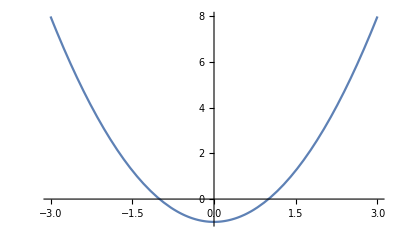

```mathematica
Plot[x^2-1,{x,-3,3}]
```

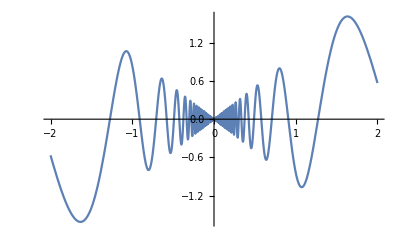

```mathematica
Plot[x Cos[10/x],{x,-2,2}]
```

```mathematica
Manipulate[x^2-1,{x,-3,3}]
```

```mathematica
Manipulate[Plot[α x Cos[10/x],{x,-2,2},PlotRange->2],{α,-2,2}]
```

### Square Root Function

```mathematica
√144
```

12

```mathematica
Sqrt[144]
```

12

### Real and Imaginary Parts of Complex Numbers

```mathematica
Re[2+3ⅈ]
```

2

```mathematica
Im[2+3ⅈ]
```

3

```mathematica
Re[(2+3ⅈ)^6]
```

2035

### Extracting Digits from a Number

```mathematica
IntegerDigits[2010]
```

{2,0,1,0}

```mathematica
IntegerDigits[2010]//MatrixForm
```

(2
0
1
0)

```mathematica
1+{2,0,1,0}
```

{3,1,2,1}

```mathematica
1+{2,0,1,0}//MatrixForm
```

(3
1
2
1)

### Programming

```mathematica
FromDigits[1+IntegerDigits[2010]]
```

3121

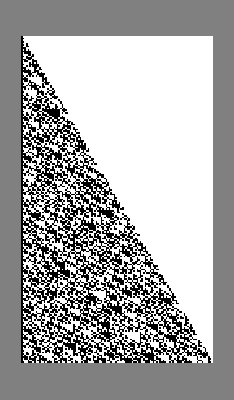

```mathematica
ArrayPlot[NestList[Function[x,IntegerDigits[Floor[3/2 FromDigits[x,2]],2]],{1,0},200],Background->Gray]
```

### Naming Things

```mathematica
θ=π/6
```

π/6

```mathematica
θ
```

π/6

```mathematica
Sin[θ]
```

1/2

```mathematica
Sin[2θ]
```

(√3)/2

```mathematica
Tan[4θ]
```

-√3

```mathematica
Clear[θ]
```

```mathematica
θ
```

θ

```mathematica
p=N[π,40]
```

3.141592653589793238462643383279502884197

```mathematica
p*2^2
```

12.56637061435917295385057353311801153679

```mathematica
Clear[p]
```

```mathematica
distance=540*miles
```

540 miles

```mathematica
time=6*hour
```

6 hour

```mathematica
rate=distance/time
```

(90 miles)/hour

```mathematica
Clear[distance,time,rate]
```

```mathematica
Length[Names["*"]]
```

7022

## Chapter 2: Working with Mathematica

## 2.2 Adding Text to Notebooks

Equation typeset without using an inline cell: f(x)-x=0

Equation typeset with using an inline cell: f(x)-x=0

## 2.8 Tips for Working Effectively

```mathematica
23^20/20^21
```

1716155831334586342923895201/2097152000000000000000000000

```mathematica
N[%]
```

0.818327

```mathematica
Sin[π/12]//N
```

0.258819

```mathematica
(x-1)(2+3x)(6-x)//Expand
```

-12-4 x+19 x^2-3 x^3

```mathematica
First@{2,4,6,8}
```

2

```mathematica
TraditionalForm@(Sin[x]^2)
```

sin^2(x)

```mathematica
1000!//Short
```

4023872600770937735437024339230039857193«2488»0000000000000000000000000000000000000000

```mathematica
20!//Timing
```

{0.00007,2432902008176640000}

```mathematica
1000000!;//Timing
```

{0.829019,Null}

```mathematica
?N
```

## 2.10 Loading Packages

Load external packages:
https://library.wolfram.com/infocenter/MathSource/AppliedMathematics/ComputerScience/

List standard packages of Mathematica

```mathematica
SetDirectory[$InstallationDirectory];
SetDirectory["AddOns"];
SetDirectory["Packages"];
FileNames[]
```

{ANOVA,Audio,BarCharts,Benchmarking,BlackBodyRadiation,Calendar,Combinatorica,ComputationalGeometry,ComputerArithmetic,Developer,EquationTrekker,ErrorBarPlots,Experimental,FiniteFields,FourierSeries,FunctionApproximations,Geodesy,GraphUtilities,HierarchicalClustering,Histograms,HypothesisTesting,LinearRegression,MultivariateStatistics,Music,NonlinearRegression,Notation,NumericalCalculus,NumericalDifferentialEquationAnalysis,PhysicalConstants,PieCharts,PlotLegends,PolyhedronOperations,Polytopes,PrimalityProving,Quaternions,RegressionCommon,ResonanceAbsorptionLines,Splines,StandardAtmosphere,StatisticalPlots,Units,VariationalMethods,VectorAnalysis,VectorFieldPlots,WorldPlot,XML}

To use a particular package

```mathematica
Needs["Units`"]
```

```mathematica
$Packages
```

{Units`,DocumentationSearch`,ProcessLink`,EntityFramework`WolframAlphaEntityStore`,EntityFramework`Utilities`,EntityFramework`ToFromEntity`,EntityFramework`Registry`,EntityFramework`Prefetch`,EntityFramework`Preferences`,EntityFramework`Predicates`,EntityFramework`OperatorForms`,EntityFramework`InterpreterCache`,EntityFramework`Formatting`,EntityFramework`Filter`,EntityFramework`FileKeyValueStore`,EntityFramework`EntityValue`,EntityFramework`EntityStore`,EntityFramework`EntityList`,EntityFramework`EntityFunctions`,EntityFramework`EntityFunction`,EntityFramework`DefaultEntityTypes`,EntityFramework`DataUtilities`,EntityFramework`DataFunctions`,EntityFramework`CustomEntity`,EntityFramework`Caching`,EntityFramework`BatchApplied`,EntityFramework`,CURLLink`URLResponseTime`,CURLLink`Utilities`,CURLInfo`,CURLLink`Cookies`,CURLLink`HTTP`,OAuthSigning`,CURLLink`URLFetch`,CURLLink`,Macros`,DocumentationSearch`Skeletonizer`,JLink`,GetFEKernelInit`,UnsupportedMessages`,RemoteEvaluate`,JSONTools`,URLUtilities`,KeychainLink`,ResourceFunctionHelpers`,UnitTable`,CloudObject`CreateUUID`,CloudObjectLoader`,NaturalLanguage`,WolframCGL`,WebAudioSearchLoader`,Templating`,NeuralNetworks`,NeuralFunctions`,MobileMessaging`,Interpreter`,IntegratedServices`,IconizeLoader`,HTTPHandling`,GeoTools`,GeometrySearchLoader`,Forms`,FormNotebook`,ExternalEvaluate`,Cryptography`,Blockchain`,Authentication`,SystemTools`,SecureShellLink`,MailLink`,IMAPLink`,ExternalStorage`,CloudDialogs`,WolframAppCatalog`,ResourceLocator`,PacletManager`,PersistenceLocations`,System`,Global`}

```mathematica
Convert[LightYear,Mile]
```

5.87863×10^12 Mile

```mathematica
Convert[16Gallon,Teaspoon]
```

12288. Teaspoon

```mathematica
Convert[1.75Liter,Jigger]
```

39.4497 Jigger

```mathematica
Convert[90Mile/Hour,Foot/Second]
```

(132 Foot)/Second

```mathematica
Names["Units`*"]//Short
```

{Abampere,Abcoulomb,Abfarad,Abhenry,«268»,Yocto,Yotta,Zepto,Zetta}

```mathematica
Take[Names["Units`*"],40;;70]
```

{BTU,Bucket,Bushel,Butt,Cable,Caliber,Calorie,Candela,Candle,Carat,Celsius,Cental,Centi,Centigrade,Centimeter,Century,CGS,Chain,ChevalVapeur,Cicero,Convert,ConvertTemperature,Cord,Coulomb,Cubit,Curie,Dalton,Day,Deca,Decade,Deci}

```mathematica
?Butt
```

```mathematica
?ConvertTemperature
```

```mathematica
ConvertTemperature[212,Fahrenheit,Celsius]
```

100

```mathematica
Convert[Butt,Gallon]
```

126. Gallon

## Chapter 3: Functions and Their Graphs

## 3.1 Defining a Function

```mathematica
Log[1]
```

0

```mathematica
f[x_]:=x^2+2x-4
```

```mathematica
f[1]
```

-1

```mathematica
f[π]
```

-4+2 π+π^2

```mathematica
inv[x_]:=1/x
```

```mathematica
inv[45]
```

1/45

```mathematica
g[x_]:=N[inv[x]]
```

```mathematica
g[45]
```

0.0222222

```mathematica
x=RandomInteger[100];{x,x,x}
```

{75,75,75}

```mathematica
x:=RandomInteger[100];{x,x,x}
```

{76,29,100}

```mathematica
?f
```

```mathematica
Clear[f]
```

```mathematica
?f
```

```mathematica
Clear["Global`*"]
```

## 3.2 Plotting a Function

```mathematica
Clear[f];
f[x_]:=x^2-2x+4
```

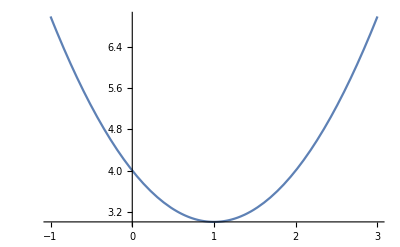

```mathematica
Plot[f[x],{x,-1,3}]
```

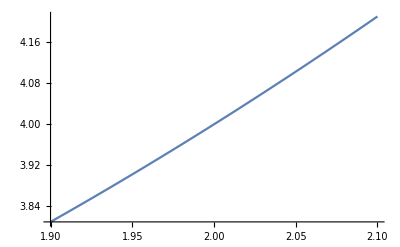

```mathematica
Plot[f[x],{x,1.9,2.1}]
```

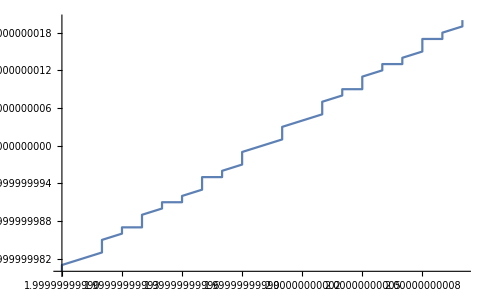

```mathematica
With[{δ=10^-10},Plot[f[x],{x,2-δ,2+δ}]]
```

The command With does not store delta after the execution of internal code.

```mathematica
δ
```

δ

```mathematica
Clear[f];
f[x_]:=(x^5-4 x^2+1)/(x-1/2)
```

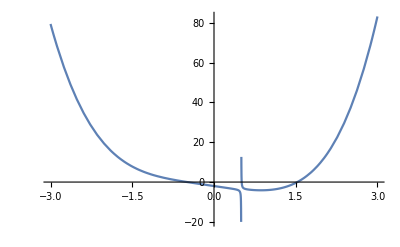

```mathematica
Plot[f[x],{x,-3,3}]
```

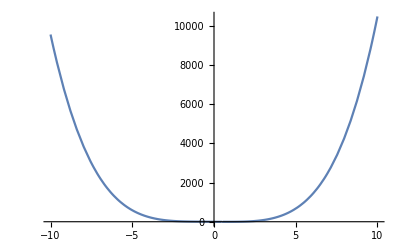

```mathematica
Plot[f[x],{x,-10,10}]
```

Mathematica has difficulty in plotting real-valued functions with negative roots:

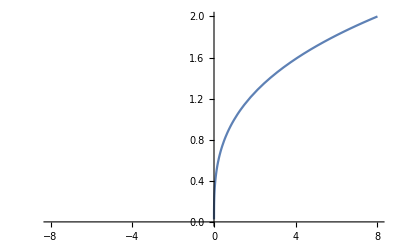

```mathematica
Plot[x^(1/3),{x,-8,8}]
```

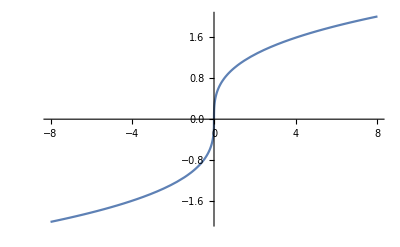

```mathematica
Plot[CubeRoot[x],{x,-8,8}]
```

Or pressing ESC cbrt ESC

```mathematica
Plot[x^(1/3),{x,-8,8}]
```

-Graphics-

```mathematica
Plot[Surd[x,3],{x,-8,8}]
```

-Graphics-

Or alternatively, press ESC surd ESC

```mathematica
Plot[x^(1/3),{x,-8,8}]
```

-Graphics-

### Exercises

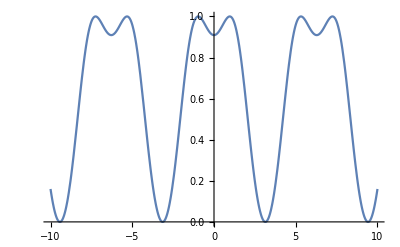

```mathematica
Plot[Sin[1+Cos[x]],{x,-10,10}]
```

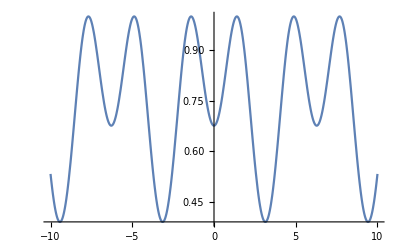

```mathematica
Plot[Sin[1.4+Cos[x]],{x,-10,10}]
```

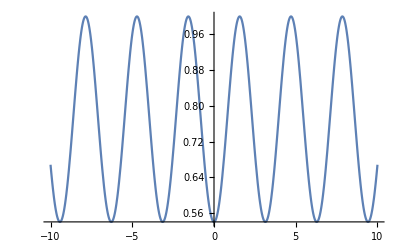

```mathematica
Plot[Sin[π/2+Cos[x]],{x,-10,10}]
```

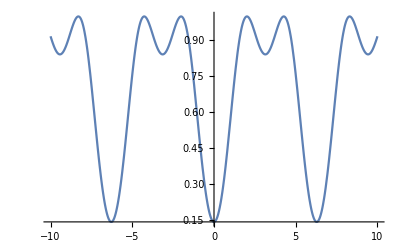

```mathematica
Plot[Sin[2+Cos[x]],{x,-10,10}]
```

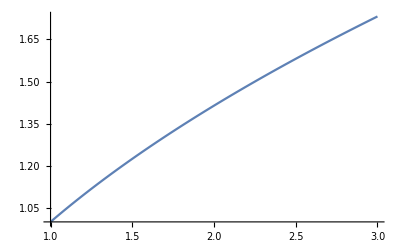

```mathematica
With[{δ=10^0},Plot[√x,{x,2-δ,2+δ}]]
```

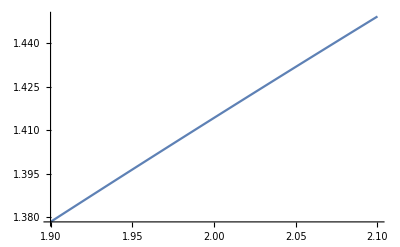

```mathematica
With[{δ=10^-1},Plot[√x,{x,2-δ,2+δ}]]
```

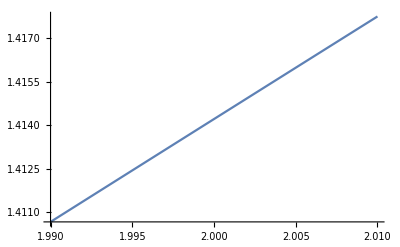

```mathematica
With[{δ=10^-2},Plot[√x,{x,2-δ,2+δ}]]
```

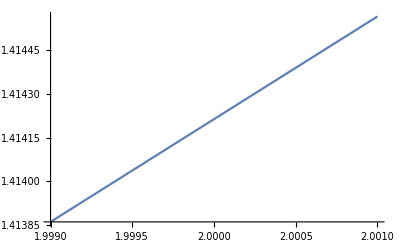

```mathematica
With[{δ=10^-3},Plot[√x,{x,2-δ,2+δ}]]
```

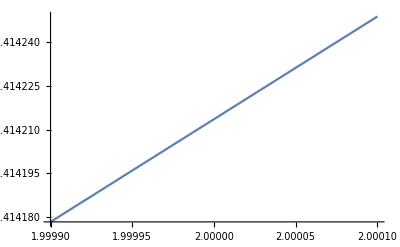

```mathematica
With[{δ=10^-4},Plot[√x,{x,2-δ,2+δ}]]
```

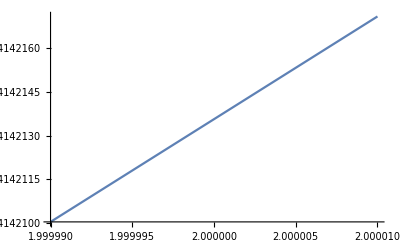

```mathematica
With[{δ=10^-5},Plot[√x,{x,2-δ,2+δ}]]
```

```mathematica
√2//N
```

1.41421

```mathematica
With[{δ=10^-20},Plot[√x,{x,2-δ,2+δ}]]
```

Plot::plld: Endpoints for x in {x,199999999999999999999/100000000000000000000,200000000000000000001/100000000000000000000} must have distinct machine-precision numerical values.

Plot[√x,{x,2-1/100000000000000000000,2+1/100000000000000000000}]

```mathematica
f[x_]:=(x^(1/5))^4;
```

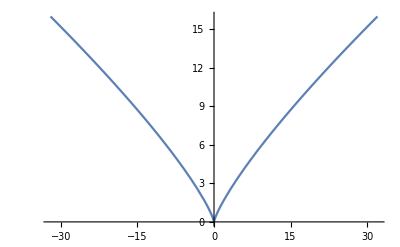

```mathematica
Plot[f[x],{x,-32,32}]
```

```mathematica
f[32]
```

16

## 3.3 Using Mathematica’s Plot Options

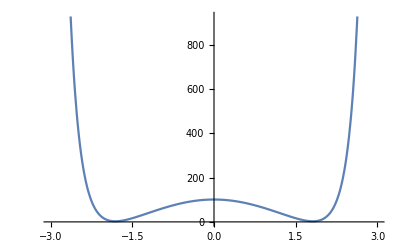

```mathematica
Plot[100 Cos[x]+ⅇ^(x^2),{x,-3,3}]
```

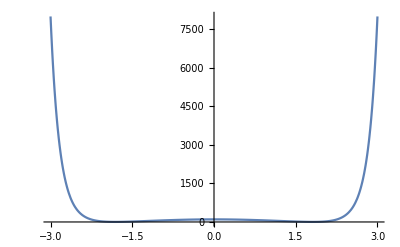

```mathematica
Plot[100 Cos[x]+ⅇ^(x^2),{x,-3,3},PlotRange->Full]
```

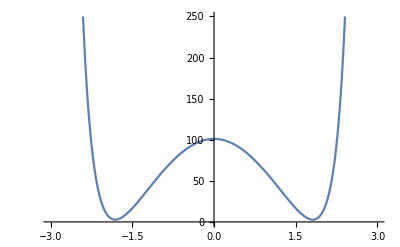

```mathematica
Plot[100 Cos[x]+ⅇ^(x^2),{x,-3,3},PlotRange->{0,250}]
```

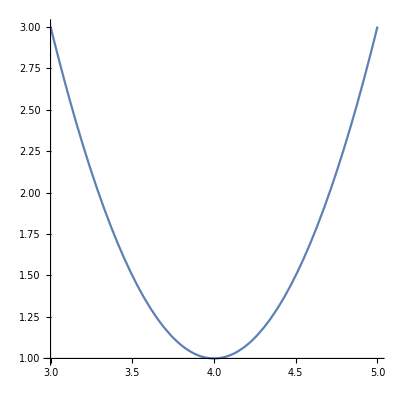

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AspectRatio->Automatic]
```

Height to width ratio of 9/16:

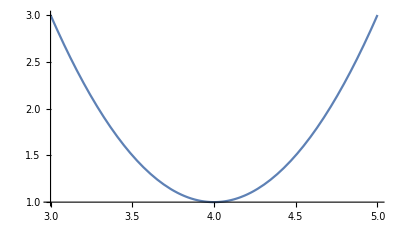

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AspectRatio->9/16]
```

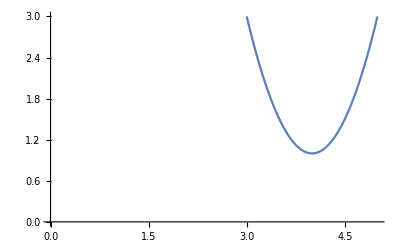

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AxesOrigin->{0,0}]
```

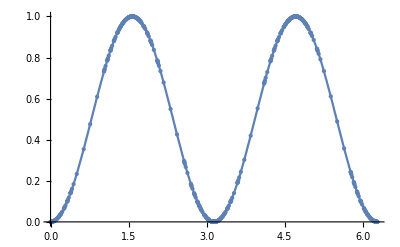

```mathematica
Plot[Sin[x]^2,{x,0,2π},Mesh->All]
```

Regularly spaced points:

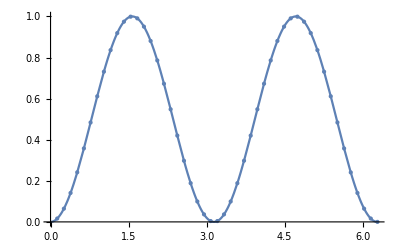

```mathematica
Plot[Sin[x]^2,{x,0,2π},Mesh->Full]
```

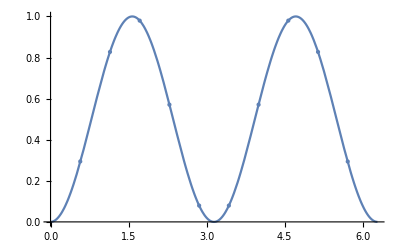

```mathematica
Plot[Sin[x]^2,{x,0,2π},Mesh->10]
```

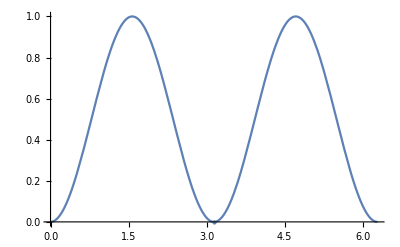

```mathematica
Plot[Sin[x]^2,{x,0,2π},Mesh->{1,2,3}]
```

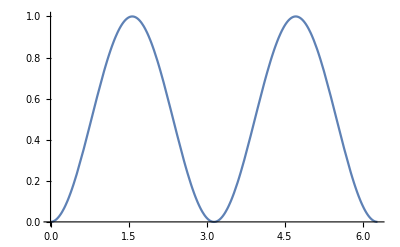

```mathematica
Plot[Sin[x]^2,{x,0,2π},MeshFunctions->{#1&}]
```

```mathematica
Plot[Sin[x]^2,{x,0,2π},MeshFunctions->{#2&}]
```

-Graphics-

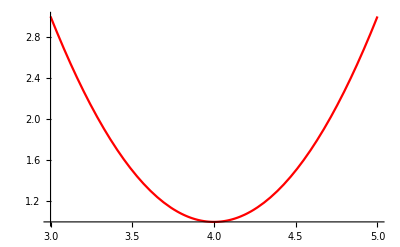

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Red]
```

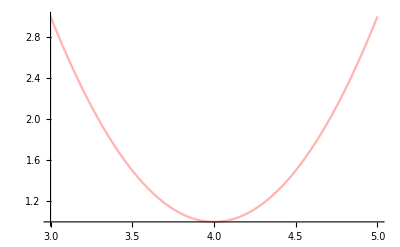

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Lighter[Red,.7]]
```

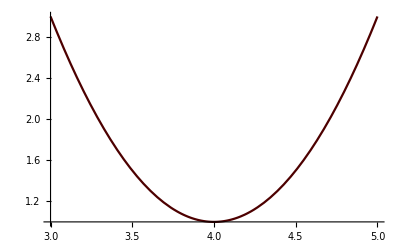

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Darker[Red,.7]]
```

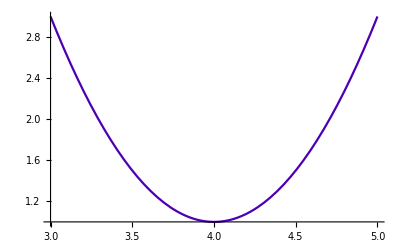

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Blend[{Blue,Red},.3]]
```

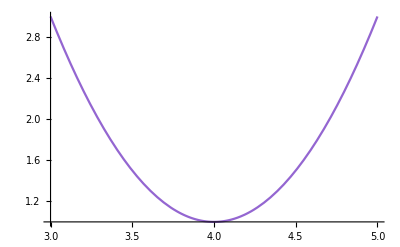

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Lighter[Blend[{Blue,Red},.3],.4]]
```

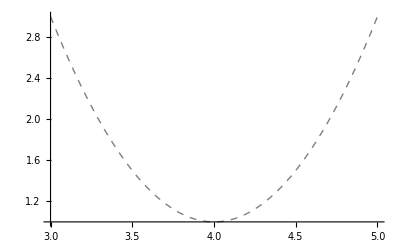

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Directive[Thick,Gray,Dashed]]
```

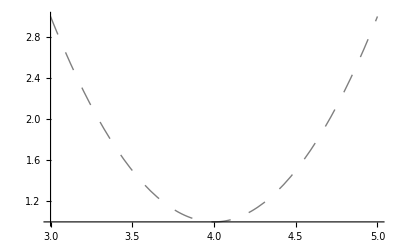

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Directive[Thick,Gray,Dashing[Large]]]
```

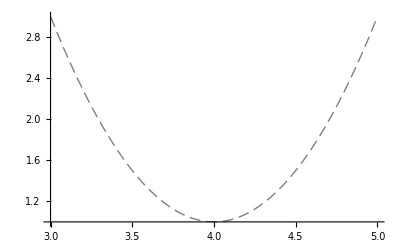

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Directive[Thick,Gray,Dashing[{.02,.01}]]]
```

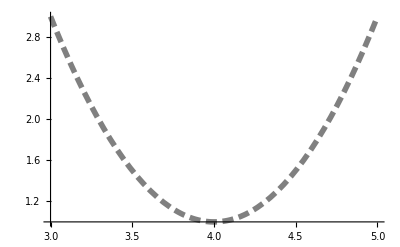

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Directive[Thickness[.01],Gray,Dashing[{.02,.01}]]]
```

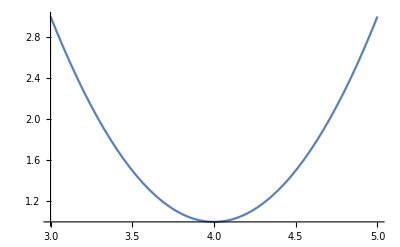

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AxesStyle->{Directive[Red,12],Blue}]
```

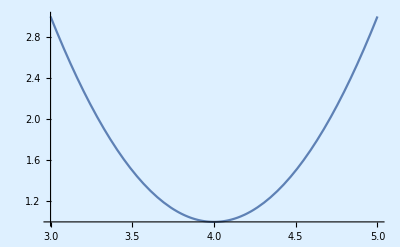

```mathematica
Plot[2(x-4)^2+1,{x,3,5},Background->LightBlue]
```

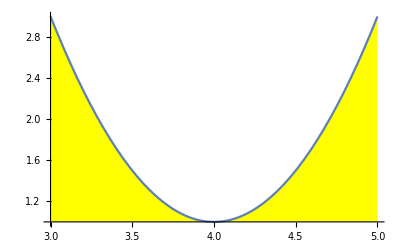

```mathematica
Plot[2(x-4)^2+1,{x,3,5},Filling->Axis,FillingStyle->Yellow]
```

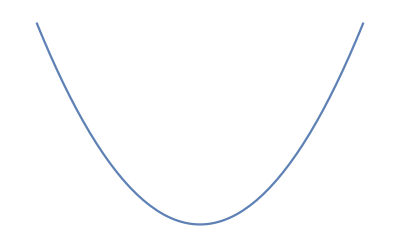

```mathematica
Plot[2(x-4)^2+1,{x,3,5},Axes->False]
```

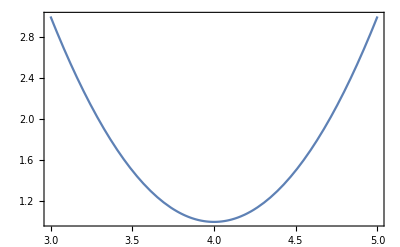

```mathematica
Plot[2(x-4)^2+1,{x,3,5},Frame->True]
```

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AxesStyle->Arrowheads[0.05]]
```

-Graphics-

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AxesStyle->Arrowheads[{-0.05,0.05}]]
```

-Graphics-

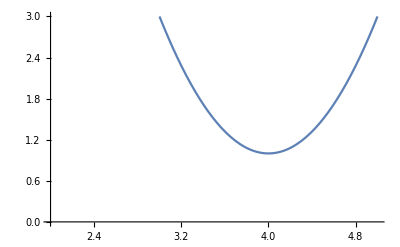

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AxesStyle->Arrowheads[.05],AxesOrigin->{2,0}]
```

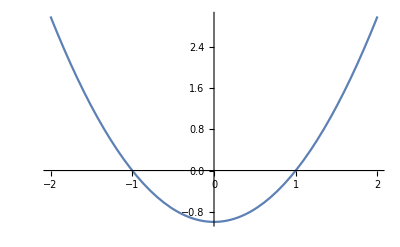

```mathematica
Plot[x^2-1,{x,-2,2},AxesStyle->Arrowheads[{-.05,.05}]]
```

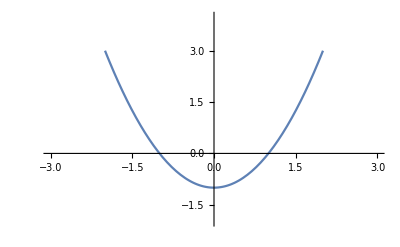

```mathematica
Plot[x^2-1,{x,-2,2},AxesStyle->Arrowheads[{-.05,.05}],PlotRange->{{-3,3},{-2,4}}]
```

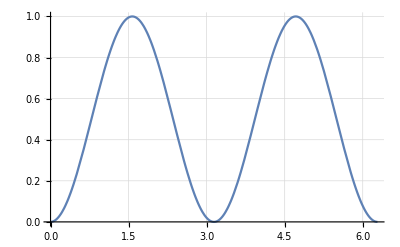

```mathematica
Plot[Sin[x]^2,{x,0,2π},GridLines->Automatic]
```

```mathematica
Plot[Sin[x]^2,{x,0,2π},GridLines->Automatic,GridLinesStyle->Directive[Thin,Gray,Dotted]]
```

-Graphics-

```mathematica
Plot[Sin[x]^2,{x,0,2π},GridLines->{{π/2,π,3 π/2,2π},{.2,.4,.6,.8,1}}]
```

-Graphics-

```mathematica
Range[0,1,.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
Plot[Sin[x]^2,{x,0,2π},GridLines->{Range[0,2π,π/8],Range[0,1,.1]}]
```

-Graphics-

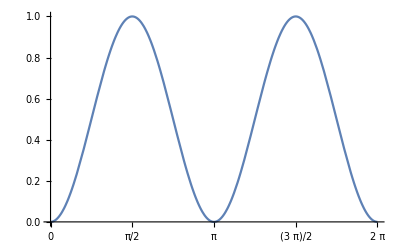

```mathematica
Plot[Sin[x]^2,{x,0,2π},GridLines->{Range[0,2π,π/8],Range[0,1,.1]},Ticks->{Range[0,2π,π/2],Automatic}]
```

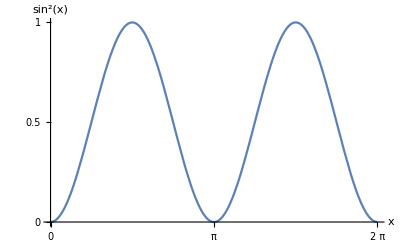

```mathematica
Plot[Sin[x]^2,{x,0,2π},Ticks->{{0,π,2π},{0,.5,1}},AxesLabel->{x,Sin[x]^2}]
```

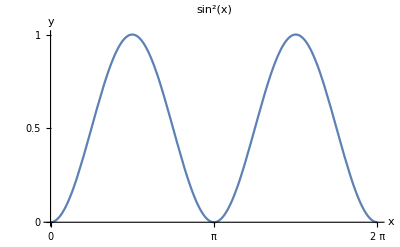

```mathematica
Plot[Sin[x]^2,{x,0,2π},Ticks->{{0,π,2π},{0,.5,1}},AxesLabel->{x,y},PlotLabel->Sin[x]^2]
```

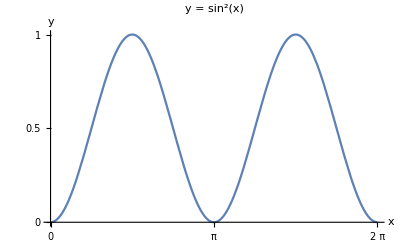

```mathematica
Plot[Sin[x]^2,{x,0,2π},Ticks->{{0,π,2π},{0,.5,1}},AxesLabel->{x,y},PlotLabel->"y = sin^2(x)"]
```

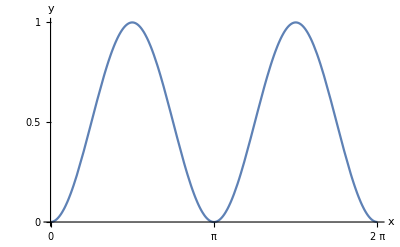
-Graphics-y = sin^2(x)

```mathematica
p=Plot[Sin[x]^2,{x,0,2π},Ticks->{{0,π,2π},{0,.5,1}},AxesLabel->{x,y}];
Labeled[p,Text["y = sin^2(x)"],Right]
```

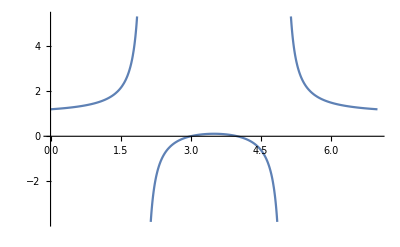

```mathematica
Plot[((x-3)(x-4))/((x-2)(x-5)),{x,0,7}]
```

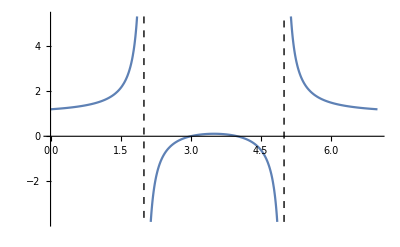

```mathematica
Plot[((x-3)(x-4))/((x-2)(x-5)),{x,0,7},Exclusions->{x==2,x==5},ExclusionsStyle->Dashed]
```

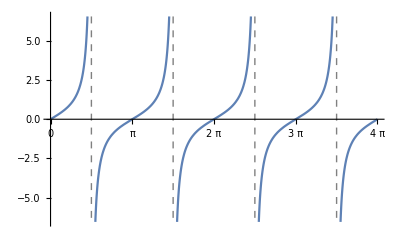

```mathematica
Plot[Tan[x],{x,0,4π},Exclusions->{Cos[x]==0},ExclusionsStyle->Directive[Gray,Dashed],Ticks->{Range[0,4π,π/2],Automatic}]
```

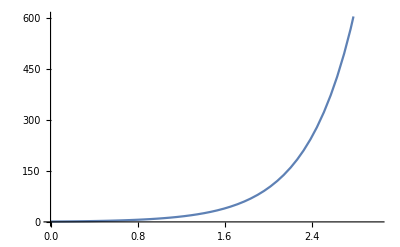

```mathematica
Plot[10^x,{x,0,3}]
```

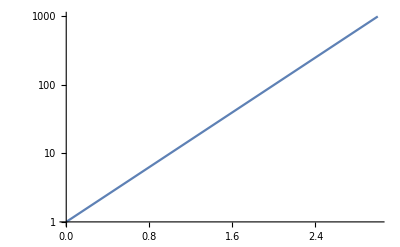

```mathematica
LogPlot[10^x,{x,0,3}]
```

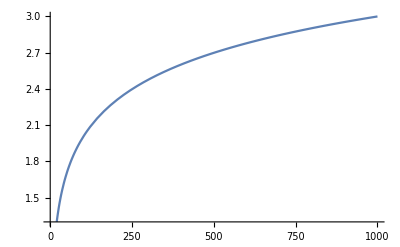

```mathematica
Plot[Log[10,x],{x,1,1000}]
```

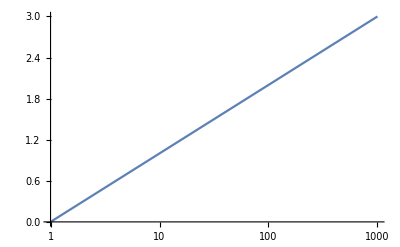

```mathematica
LogLinearPlot[Log[10,x],{x,1,1000}]
```

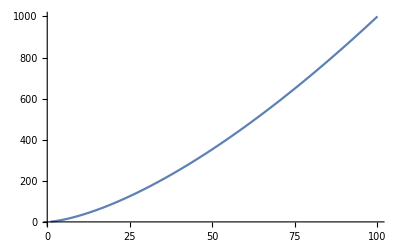

```mathematica
Plot[x^(3/2),{x,1,100}]
```

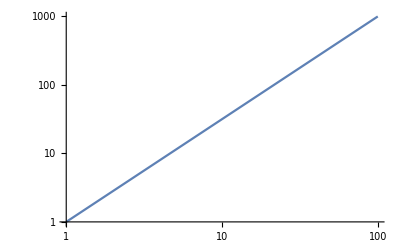

```mathematica
LogLogPlot[x^(3/2),{x,1,100}]
```

### Exercises

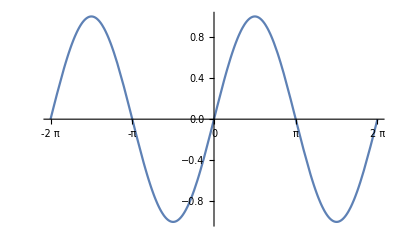

```mathematica
Plot[Sin[x],{x,-2π,2π},GridLines->{Range[-2π,2π,π/4],Range[-1,1,.2]},GridLinesStyle->Lighter[Gray],Ticks->{Range[-2π,2π,π],Automatic}]
```

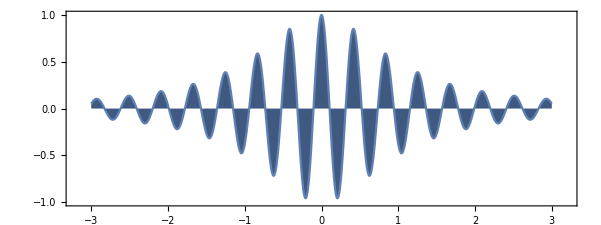

```mathematica
Plot[Cos[15x]/(1+x^2),{x,-3,3},Axes->False,Frame->{{True,False},{True,False}},Filling->Axis,FillingStyle->Hue[.6,.5,.5],PlotRange->{{-3.2,3.2},{-1,1}},AspectRatio->6/16]
```

```mathematica
RGBColor[.2,.8,.8]
```

RGBColor[0.2, 0.8, 0.8]

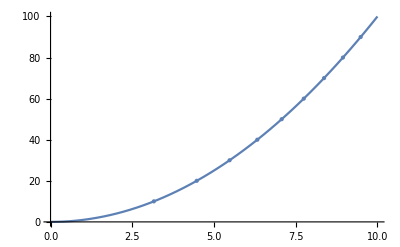

```mathematica
Plot[x^2,{x,0,10},Mesh->9,MeshFunctions->{#2&},GridLines->{√Range[0,100,10],Range[0,100,10]}]
```

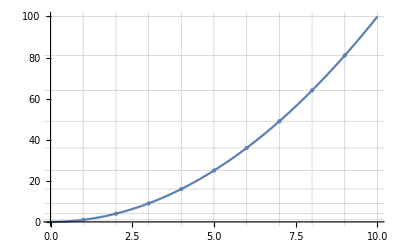

```mathematica
Plot[x^2,{x,0,10},Mesh->9,MeshFunctions->{#1&},GridLines->{Range[0,10,1],(Range[0,10,1])^2}]
```

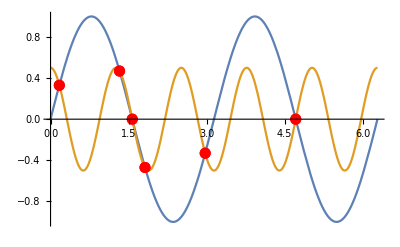

```mathematica
Plot[{Sin[2x],1/2 Cos[5x]},{x,0,2π},Mesh->{{0.}},MeshFunctions->{Sin[2#]-1/2 Cos[5#]&},MeshStyle->Directive[PointSize[0.02],Red]]
```

## Chapter 6: Multivariable Calculus

## 6.1 Vectors

```mathematica
Clear[u,v,i,j];
```

```mathematica
{2,5}+{17,-4}
```

{19,1}

```mathematica
-4{2,5}
```

{-8,-20}

```mathematica
i={1,0};
j={0,1};
2i+5j
```

{2,5}

```mathematica
{3,-57,8}+{57,-3,π/4}
```

{60,-60,8+π/4}

```mathematica
{Subscript[u, 1],Subscript[u, 2]}.{Subscript[v, 1],Subscript[v, 2]}
```

u_1 v_1+u_2 v_2

```mathematica
{3,4}.{4,5}
```

32

```mathematica
Norm[{3,4}]
```

5

```mathematica
Norm[{Subscript[u, 1],Subscript[u, 2]}]
```

√(Abs[u_1]^2+Abs[u_2]^2)

```mathematica
Simplify[Norm[{Subscript[u, 1],Subscript[u, 2]}],{Subscript[u, 1],Subscript[u, 2]}∈Reals]
```

√(u_1^2+u_2^2)

```mathematica
√({Subscript[u, 1],Subscript[u, 2]}.{Subscript[u, 1],Subscript[u, 2]})
```

√(u_1^2+u_2^2)

```mathematica
u={2,4};v={9,-13};
ArcCos[(u.v)/(Norm[u]Norm[v])]//N
```

2.0724

```mathematica
%/Degree
```

118.74

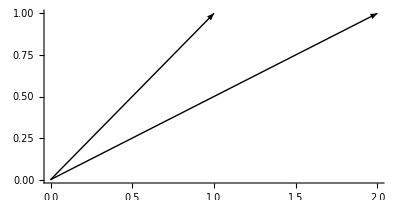

```mathematica
Graphics[{Arrow[{{0,0},{1,1}}],Arrow[{{0,0},{2,1}}]},Axes->True]
```

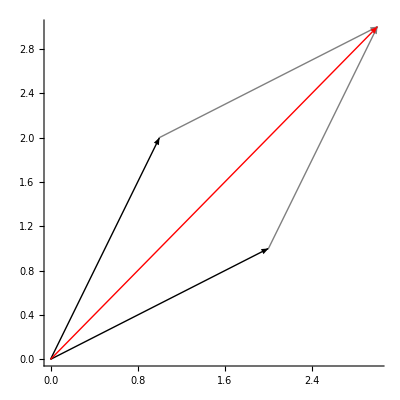

```mathematica
Graphics[{
Arrow[{{0,0},{1,2}}],Arrow[{{0,0},{2,1}}],
{Gray,Arrow[{{1,2},{3,3}}],Arrow[{{2,1},{3,3}}]},
{Red,Arrow[{{0,0},{3,3}}]}
},PlotRange->{{0,3},{0,3}},Axes->True]
```

```mathematica
Manipulate[Graphics[{
Arrow[{{0,0},u}],Arrow[{{0,0},v}],
{Gray,Arrow[{u,u+v}],Arrow[{v,u+v}]},
{Red,Arrow[{{0,0},u+v}]}
},PlotRange->3,Axes->True,Ticks->None],
{{u,{1,2}},Locator,Appearance->None},
{{v,{2,1}},Locator,Appearance->None}]
```

```mathematica
Clear[u,v];Cross[{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]},{Subscript[v, 1],Subscript[v, 2],Subscript[v, 3]}]
```

{-u_3 v_2+u_2 v_3,u_3 v_1-u_1 v_3,-u_2 v_1+u_1 v_2}

```mathematica
Cross[{1,3,5},{7,9,11}]
```

{-12,24,-12}

```mathematica
{1,3,5}×{7,9,11}
```

{-12,24,-12}

### Exercises

```mathematica
u={2,-1,1};v={3,2,1};
1-((u.v)/(Norm[u]Norm[v]))^2
```

59/84

```mathematica
Sign[(u.v)/(Norm[u]Norm[v])]
```

1

```mathematica
Clear[u,v];Dot[{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]},{Subscript[v, 1],Subscript[v, 2],Subscript[v, 3]}]
```

u_1 v_1+u_2 v_2+u_3 v_3

```mathematica
Inner[Times,{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]},{Subscript[v, 1],Subscript[v, 2],Subscript[v, 3]},Plus]
```

u_1 v_1+u_2 v_2+u_3 v_3

```mathematica
Clear[u,v];
Simplify[(Norm[u+v])^2+(Norm[u-v])^2]
```

Norm[u-v]^2+Norm[u+v]^2

```mathematica
==2(Norm[u])^2+2(Norm[v])^2
```

## 6.2 Real-Valued Functions of Two or More Variables

```mathematica
f[x_,y_]:=Sin[x^2-y^2]
```

```mathematica
Clear[f,x,y];
f=Sin[x^2-y^2];
```

```mathematica
Clear[g,x,y,z];
g=x^2 y^3-3x z;
```

Use replacement rules to evaluate a function f(0,√(π/4))

```mathematica
f/.{x->0,y->√(π/4)}
```

-1/(√2)

```mathematica
f/.{x->1-π,y->1+π}
```

Sin[(1-π)^2-(1+π)^2]

```mathematica
Simplify[%]
```

0

```mathematica
Plot3D[f,{x,-2,2},{y,-1,1}]
```

-Graphics3D-

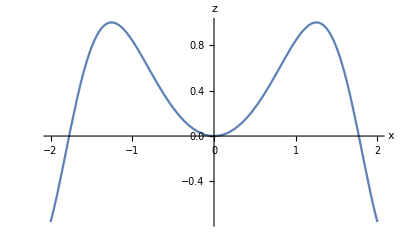

```mathematica
Plot[f/.y->0,{x,-2,2},AxesLabel->{x,z}]
```

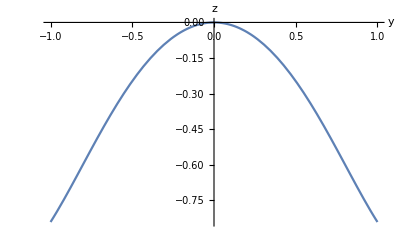

```mathematica
Plot[f/.x->0,{y,-1,1},AxesLabel->{y,z}]
```

```mathematica
Table[Plot3D[ⅇ^Sin[x y],{x,-π,π},{y,-π,π},Mesh->m,MaxRecursion->4],{m,{None,All}}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Table[Plot3D[(x^2 y^5-x^5 y^2)/100+ⅇ^(-(x^2+y^2)),{x,-3,3},{y,-3,3},ClippingStyle->k],{k,{Automatic,None}}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[(x^2 y^5-x^5 y^2)/100+ⅇ^(-(x^2+y^2)),{x,-3,3},{y,-3,3},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x Cos[y]],{x,-6,6},{y,-3,3},BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x Cos[y]],{x,-6,6},{y,-3,3},BoxRatios->1]
```

-Graphics3D-

```mathematica
Plot3D[(x^2 y^5-x^5 y^2)/100+ⅇ^(-(x^2+y^2)),{x,-3,3},{y,-3,3},BoxRatios->{1,1,2}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x Cos[y]],{x,-6,6},{y,-3,3},BoxRatios->Automatic,Boxed->False,Axes->{False,False,True},AxesEdge->{Automatic,Automatic,{-1,-1}}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x Cos[y]],{x,-6,6},{y,-3,3},BoxRatios->Automatic,ViewPoint->{3,0,1}]
```

-Graphics3D-

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
Plot3D[ⅇ^(-(x^2+y^2)),{x,-3,3},{y,-3,3},BoxRatios->Automatic,ColorFunction->"DarkTerrain",PlotRange->All,Mesh->None]
```

-Graphics3D-